# Calculations for well-defined.tex

```mathematica
SetDirectory[NotebookDirectory[]];
<<tools.m;
```

```mathematica
cleanTools[];
```

```mathematica
paramCount[x_]:=Length[Cases[Variables[x],p[_]]];
```

### A2 func

#### define ansatz

```mathematica
alg=a2[];
vars=sortInverse[a2Xs[x1,x2]];
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
ansatzB2b2 = Flatten[Table[wedge[cb2[vars[[i]]],cb2[vars[[j]]]],{i,Length[vars]},{j,i-1}]];
```

```mathematica
ansatzB3c = Flatten[Table[tensor[cb3[vars[[i]]],vars[[j]]],{i,Length[vars]},{j,Length[vars]}]];
```

```mathematica
ansatz=p/@Range[Length[#]].#&@Join[ansatzB2b2,ansatzB3c];
```

```mathematica
paramCount[ansatz]
```

35

linear independence

```mathematica
ansatz=ansatz/.Thread[Variables[(#[[2]]&/@fit[b2b2[ansatz]])]->0];
```

```mathematica
paramCount[ansatz]
```

31

integrability

```mathematica
solnIntegrability=fit[delta[ansatz]]
```

{p[1]→p[34],p[2]→p[34],p[3]→-p[34],p[4]→p[34],p[5]→-p[34],p[6]→p[34],p[12]→-p[34],p[13]→-p[34],p[14]→0,p[15]→0,p[16]→-p[34],p[18]→0,p[19]→-p[34],p[20]→0,p[21]→p[34],p[22]→0,p[24]→0,p[25]→p[34],p[26]→0,p[27]→p[34],p[28]→0,p[30]→-p[34],p[31]→0,p[32]→0,p[33]→p[34]}

```mathematica
ansatz=ansatz/.solnIntegrability;paramCount[ansatz]
```

6

#### symmetric function

ansatz already symmetric at B2b2 level:

```mathematica
Expand[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

```mathematica
solnSymB3c=fit[Expand[b3c[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]]
```

{p[11]→-p[35],p[17]→p[35],p[23]→-p[35],p[29]→p[35]}

```mathematica
ansatzSym=ansatz/.solnSymB3c;paramCount[ansatzSym]
```

2

we can fix one more parameter by imposing that the function flip sign under {x1→1/x2, x2→1/x1}:

```mathematica
b2b2[ansatzSym+(ansatzSym/.{x1->1/x2,x2->1/x1})]//Expand
```

0

```mathematica
solnFlipB3c=fit[b3c[ansatzSym+(ansatzSym/.{x1->1/x2,x2->1/x1})]//Expand]
```

{p[35]→0}

```mathematica
ansatzSym/.solnFlipB3c/.p[_]:>1
```

-tensor[cb3[x1],x2]-tensor[cb3[x1],(x1 x2)/(1+x1)]-tensor[cb3[x2],x1]-tensor[cb3[x2],x1 (1+x2)]+tensor[cb3[(x1 x2)/(1+x1)],x1]+tensor[cb3[(x1 x2)/(1+x1)],(1+x1+x1 x2)/x2]+tensor[cb3[x1 (1+x2)],x2]-tensor[cb3[x1 (1+x2)],(1+x1+x1 x2)/x2]+tensor[cb3[(1+x1+x1 x2)/x2],(x1 x2)/(1+x1)]+tensor[cb3[(1+x1+x1 x2)/x2],x1 (1+x2)]+wedge[cb2[x2],cb2[x1]]+wedge[cb2[(x1 x2)/(1+x1)],cb2[x1]]-wedge[cb2[(x1 x2)/(1+x1)],cb2[x2]]+wedge[cb2[x1 (1+x2)],cb2[x1]]-wedge[cb2[x1 (1+x2)],cb2[x2]]+wedge[cb2[x1 (1+x2)],cb2[(x1 x2)/(1+x1)]]

and so now we can define

```mathematica
a2Func[x1_,x2_]:=-tensor[cb3[x1],x2]-tensor[cb3[x1],(x1 x2)/(1+x1)]-tensor[cb3[x2],x1]-tensor[cb3[x2],x1 (1+x2)]+tensor[cb3[(x1 x2)/(1+x1)],x1]+tensor[cb3[(x1 x2)/(1+x1)],(1+x1+x1 x2)/x2]+tensor[cb3[x1 (1+x2)],x2]-tensor[cb3[x1 (1+x2)],(1+x1+x1 x2)/x2]+tensor[cb3[(1+x1+x1 x2)/x2],(x1 x2)/(1+x1)]+tensor[cb3[(1+x1+x1 x2)/x2],x1 (1+x2)]+wedge[cb2[x2],cb2[x1]]+wedge[cb2[(x1 x2)/(1+x1)],cb2[x1]]-wedge[cb2[(x1 x2)/(1+x1)],cb2[x2]]+wedge[cb2[x1 (1+x2)],cb2[x1]]-wedge[cb2[x1 (1+x2)],cb2[x2]]+wedge[cb2[x1 (1+x2)],cb2[(x1 x2)/(1+x1)]]//cleanCoproducts;
```

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[Expand[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]]
```

{p[34]→0}

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

5

```mathematica
solnAntiSymB3c=fit[Expand[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]]]
```

{p[11]→0,p[17]→0,p[23]→0,p[29]→0,p[35]→0}

```mathematica
ansatzAntiSym=ansatzAntiSym/.solnAntiSymB3c;paramCount[ansatzAntiSym]
```

0

### A3 func in terms of A2

#### define ansatz

```mathematica
alg=a3[];
sub=a2;
subFunc=a2Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub]
```

{{x1,x2},{x1,x2 (1+x3)},{x2,x3},{(x1 x2)/(1+x1),x3},{x1 (1+x2),(x2 x3)/(1+x2)},{x2/(1+x1+x1 x2),((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3)}}

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

6

linear independence

```mathematica
Length[fit[b2b2[ansatz]]]-paramCount[ansatz]
```

0

```mathematica
Length[fit[b3c[ansatz]]]-paramCount[ansatz]
```

0

```mathematica
fit[b2b2[ansatz-(ansatz/.{x1->1/x3,x2->1/x2,x1->1/x3})]]
```

{p[1]→0,p[2]→0,p[3]→0,p[4]→0,p[5]→0,p[6]→0}

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→p[6],p[2]→p[6],p[3]→p[6],p[4]→p[6],p[5]→p[6]}

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

1

```mathematica
Expand[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

surprising! i did not realize that there was a symmetric a3 function. does it have a particularly nice -- ideally local -- coproduct?

```mathematica
goodPairs=Union[sortInverse/@Select[Subsets[a3Xs[],{2}],(pb[a3[]]@@#)≠I&]];
```

```mathematica
target=(p/@Range[Length[goodPairs]]).(wedge[cb2[#1],cb2[#2]]&@@#&/@goodPairs);
```

```mathematica
fit[b2b2[target-(ansatzSym/.p[_]:>1)]]
```

{}

so it does not have a “nice” coproduct -- it is just the symmetric sum of A2s with no additional “special sauce”

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[Expand[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]]
```

{p[1]→-p[6],p[2]→p[6],p[3]→-p[6],p[4]→p[6],p[5]→-p[6]}

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

1

```mathematica
Expand[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

let’s define this as *the* a3 function

```mathematica
a3Func[x1_,x2_,x3_]:=wedge[cb2[x1],cb2[x3]]+wedge[cb2[x2/(1+x1+x1 x2)],cb2[(x1 x2 x3)/(1+x1+x1 x2)]]-wedge[cb2[x1 (1+x2+x2 x3)],cb2[x3/(1+x2+x2 x3)]]+(1/2(- a2Func[x1,x2]+ a2Func[x1,x2 (1+x3)]- a2Func[x2,x3]+ a2Func[(x1 x2)/(1+x1),x3]- a2Func[x1 (1+x2),(x2 x3)/(1+x2)]+ a2Func[x2/(1+x1+x1 x2),((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3)])/.wedge[__]:>0)//cleanCoproducts;
```

### A4 func in terms of A2

#### define ansatz

```mathematica
alg=a4[];
sub=a2;
subFunc=a2Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

21

linear independence

```mathematica
Length[fit[b2b2[ansatz]]]-paramCount[ansatz]
```

0

```mathematica
Length[fit[b3c[ansatz]]]-paramCount[ansatz]
```

0

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→p[18],p[2]→p[19],p[3]→p[18],p[4]→p[19],p[5]→p[21],p[6]→p[21],p[7]→p[21],p[8]→p[21],p[9]→p[19],p[10]→p[18],p[11]→p[19],p[12]→p[18],p[13]→p[19],p[14]→p[18],p[15]→p[21],p[16]→p[19],p[17]→p[18],p[20]→p[21]}

```mathematica
Tally[(p/@Range[21])//.solnSymB2b2]
```

{{p[18],7},{p[19],7},{p[21],7}}

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

3

```mathematica
Expand[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

what about imposing the “flip” symmetry?

```mathematica
fit[b3c[ansatzSym+(ansatzSym/.Thread[{x1,x2,x3,x4}->{1/x4,1/x3,1/x2,1/x1}])]]
```

Part::partw: Part 2 of {{}} does not exist.

If[If[{-1+RowReduce[Transpose[Transpose[{{}}⟦2⟧,{}]]]}=={0},0,1]==1,Table[With[{pos$=Position[matSolve$3146⟦iii⟧,1,1,1]⟦1,1⟧},x$3146⟦pos$⟧→-matSolve$3146⟦iii,pos$+1;;-1⟧.Append[x$3146,-1]⟦pos$+1;;-1⟧],{iii,Length[matSolve$3146]}],{}]

all already satisfy this symmetry. what does their coproduct look like?

```mathematica
goodPairs=Union[sortInverse/@Select[Subsets[a4Xs[],{2}],(pb[a4[]]@@#)≠I&]];
```

```mathematica
target=(p/@(Range[Length[goodPairs]]+3)).(wedge[cb2[#1],cb2[#2]]&@@#&/@goodPairs);
```

```mathematica
ansatzSym=ansatzSym/.{p[18]->p[1],p[19]->p[2],p[21]->p[3]};
```

```mathematica
solnLocal=fit[b2b2[target-ansatzSym]];
```

```mathematica
ansatzSym/.solnLocal
```

0

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→0,p[2]→0,p[3]→0,p[4]→0,p[5]→0,p[6]→0,p[7]→0,p[8]→0,p[9]→0,p[10]→0,p[11]→0,p[12]→0,p[13]→0,p[14]→0,p[15]→0,p[16]→0,p[17]→0,p[18]→0,p[19]→0,p[20]→0,p[21]→0}

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

1

```mathematica
Expand[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

let’s define this as *the* a3 function

```mathematica
a3Func[x1_,x2_,x3_]:=wedge[cb2[x1],cb2[x3]]+wedge[cb2[x2/(1+x1+x1 x2)],cb2[(x1 x2 x3)/(1+x1+x1 x2)]]-wedge[cb2[x1 (1+x2+x2 x3)],cb2[x3/(1+x2+x2 x3)]]+(1/2(- a2Func[x1,x2]+ a2Func[x1,x2 (1+x3)]- a2Func[x2,x3]+ a2Func[(x1 x2)/(1+x1),x3]- a2Func[x1 (1+x2),(x2 x3)/(1+x2)]+ a2Func[x2/(1+x1+x1 x2),((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3)])/.wedge[__]:>0)//cleanCoproducts;
```

### A4 func in terms of A3

#### define ansatz

```mathematica
alg=a4[];
sub=a3;
subFunc=a3Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

7

linear independence

```mathematica
Length[fit[b2b2[ansatz]]]-paramCount[ansatz]
```

-1

```mathematica
Length[fit[b3c[ansatz]]]-paramCount[ansatz]
```

-1

```mathematica
solnLinIndep=Thread[Variables[(#[[2]]&/@fit[b2b2[ansatz]])]->0]
```

{p[7]→0}

```mathematica
ansatz=ansatz/.solnLinIndep;paramCount[ansatz]
```

6

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→0,p[2]→0,p[3]→0,p[4]→0,p[5]→0,p[6]→0}

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→0,p[2]→0,p[3]→0,p[4]→0,p[5]→0,p[6]→0}

### D4 func in terms of A2

#### define ansatz

```mathematica
alg=d4[];
sub=a2;
subFunc=a2Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

36

linear independence

```mathematica
Length[fit[b2b2[ansatz]]]-paramCount[ansatz]
```

-2

```mathematica
Length[fit[b3c[ansatz]]]-paramCount[ansatz]
```

0

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→p[31],p[2]→p[30],p[3]→p[32],p[4]→p[31],p[5]→p[33],p[6]→p[27],p[7]→p[35],p[8]→p[36],p[9]→p[34],p[10]→p[29],p[11]→p[32],p[12]→p[30],p[13]→p[31],p[14]→p[35],p[15]→p[34],p[16]→p[27],p[17]→p[29],p[18]→p[33],p[19]→p[35],p[20]→p[36],p[21]→p[29],p[22]→p[33],p[23]→p[32],p[24]→p[34],p[25]→p[30],p[26]→p[27],p[28]→p[36]}

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

9

```mathematica
Expand[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

```mathematica
Tally[(p/@Range[36])//.solnSymB2b2]
```

{{p[31],4},{p[30],4},{p[32],4},{p[33],4},{p[27],4},{p[35],4},{p[36],4},{p[34],4},{p[29],4}}

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→p[31],p[2]→p[25],p[3]→p[32],p[4]→-p[25]-p[30]-p[31],p[5]→-p[25]+p[28]-p[30]-p[33]+p[36],p[6]→-p[27]-p[28]-p[36],p[7]→p[35],p[8]→p[36],p[9]→-p[25]+p[28]-p[30]-p[34]+p[36],p[10]→-p[28]-p[29]-p[36],p[11]→p[25]+p[30]-p[32],p[12]→p[30],p[13]→-p[25]-p[30]-p[31],p[14]→p[25]-p[28]+p[30]-p[35]-p[36],p[15]→p[34],p[16]→-p[27]-p[28]-p[36],p[17]→-p[28]-p[29]-p[36],p[18]→p[33],p[19]→p[25]-p[28]+p[30]-p[35]-p[36],p[20]→p[28],p[21]→p[29],p[22]→-p[25]+p[28]-p[30]-p[33]+p[36],p[23]→p[25]+p[30]-p[32],p[24]→-p[25]+p[28]-p[30]-p[34]+p[36],p[26]→p[27]}

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

11

```mathematica
solnAntiSymB3c=fit[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[25]→-p[30],p[28]→-p[36]}

```mathematica
ansatzAntiSym=ansatzAntiSym/.solnAntiSymB3c;paramCount[ansatzAntiSym]
```

9

### D4 func in terms of A3

#### define ansatz

```mathematica
alg=d4[];
sub=a3;
subFunc=a3Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs)//cleanCoproducts//cleanWedge;
```

```mathematica
ansatzExp=(p/@Range[Length[subs]]).(A3@@@subs);
```

```mathematica
paramCount[ansatz]
```

12

linear independence

```mathematica
Length[fit[b2b2[ansatz]]]-paramCount[ansatz]
```

-3

```mathematica
Length[fit[b3c[ansatz]]]-paramCount[ansatz]
```

-1

```mathematica
eqsB2b2=genEqs[b2b2[ansatz]];
```

```mathematica
eqsB3c=genEqs[b3c[ansatz]];
```

```mathematica
solnZero=Solve[Thread[Join[eqsB2b2,eqsB3c]==0]][[1]];
```

```mathematica
solnLinIndep=Thread[Variables[(#[[2]]&/@solnZero)]->0]
```

{p[1]→0}

```mathematica
ansatz=ansatz/.solnLinIndep;paramCount[ansatz]
```

11

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[2]→p[11],p[3]→-p[11],p[4]→0,p[5]→0,p[6]→-p[11],p[7]→-p[12],p[8]→p[12],p[9]→-p[12],p[10]→0}

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

2

```mathematica
Expand[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

0

```mathematica
hmSym1=Collect[ansatzSym,p[_]][[1]]/.p[_]:>1;
hmSym2=Collect[ansatzSym,p[_]][[2]]/.p[_]:>1;
```

```mathematica
hmSym1//b2b2
```

0

```mathematica
hmSym2//b2b2
```

0

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[1]→p[10],p[2]→p[11],p[3]→p[6],p[4]→p[5],p[7]→p[9],p[8]→p[12]}

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

6

```mathematica
solnAntiSymB3c=fit[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]]
```

{p[5]→p[9]+p[10]-p[12],p[6]→-p[9]+p[11]+p[12]}

```mathematica
ansatzAntiSym=ansatzAntiSym/.solnAntiSymB3c;paramCount[ansatzAntiSym]
```

4

```mathematica
solnFlipB2b2=fit[b2b2[ansatzAntiSym-(ansatzAntiSym/.{x3->x4,x4->x3})]]
```

{p[9]→-p[12],p[10]→p[11]+2 p[12]}

```mathematica
ansatzAntiSymFlip=ansatzAntiSym/.solnFlipB2b2;paramCount[ansatzAntiSymFlip]
```

2

```mathematica
solnFlipB3c=fit[b3c[ansatzAntiSymFlip-(ansatzAntiSymFlip/.{x3->x4,x4->x3})]]
```

Part::partw: Part 1 of {} does not exist.

{}

```mathematica
Collect[ansatzExp/.solnAntiSymB2b2/.solnAntiSymB3c/.solnFlipB2b2,p[_]]
```

(A3[x1,x2,x3]+A3[x1,x2,x4]+A3[x1,x2 (1+x3),x4]+A3[x1,x2 (1+x4),x3]+A3[(x1 x2 x3)/(1+x1+x1 x2),(x2 x4)/((1+x2) (1+x1+x1 x2+x1 x2 x4)),(1+x1+x1 x2)/x2]+A3[x1 (1+x2+x2 x3),(x2 x4)/(1+x2),x3/(1+x2+x2 x3)]+A3[(x1 x2 x4)/(1+x1+x1 x2),(x2 x3)/((1+x2) (1+x1+x1 x2+x1 x2 x3)),(1+x1+x1 x2)/x2]+A3[x1 (1+x2+x2 x4),(x2 x3)/(1+x2),x4/(1+x2+x2 x4)]) p[11]+(2 A3[x1,x2,x3]+2 A3[x1,x2 (1+x3),x4]-A3[1/x3,x2 (1+x3),x4]+A3[1/x3,(x1 x2 (1+x3))/(1+x1),x4]-A3[(1+x2)/(x2 x3),x1 (1+x2+x2 x3),(x2 x4)/(1+x2)]+2 A3[x1 (1+x2+x2 x3),(x2 x4)/(1+x2),x3/(1+x2+x2 x3)]+2 A3[(x1 x2 x4)/(1+x1+x1 x2),(x2 x3)/((1+x2) (1+x1+x1 x2+x1 x2 x3)),(1+x1+x1 x2)/x2]+A3[(1+x1+x1 x2+x1 x2 x3+x1 x2 x4+x1 x2 x3 x4)/((1+x1) x3),(x2 (1+x3))/(1+x1+x1 x2+x1 x2 x3),((1+x1) x4)/(1+x1+x1 x2+x1 x2 x3+x1 x2 x4+x1 x2 x3 x4)]) p[12]

check that the antisym ansatz is still antisym for other redundant seeds

```mathematica
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[3]]);
```

```mathematica
b2b2[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]//Expand
```

0

```mathematica
b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]//fit
```

Part::partw: Part 1 of {} does not exist.

{}

```mathematica
sortInverse[Together[d4Xs[1/x4,1/x2,1/x3,1/x1]]]===sortInverse[Together[d4Xs[]]]
```

False

```mathematica
d4Func[x1_,x2_,x3_,x4_]:=a3Func[x1,x2,x3]+a3Func[x1,x2,x4]+a3Func[x1,x2 (1+x3),x4]+a3Func[x1,x2 (1+x4),x3]+a3Func[(x1 x2 x3)/(1+x1+x1 x2),(x2 x4)/((1+x2) (1+x1+x1 x2+x1 x2 x4)),(1+x1+x1 x2)/x2]+a3Func[x1 (1+x2+x2 x3),(x2 x4)/(1+x2),x3/(1+x2+x2 x3)]+a3Func[(x1 x2 x4)/(1+x1+x1 x2),(x2 x3)/((1+x2) (1+x1+x1 x2+x1 x2 x3)),(1+x1+x1 x2)/x2]+a3Func[x1 (1+x2+x2 x4),(x2 x3)/(1+x2),x4/(1+x2+x2 x4)];
```

### D5 func in terms of D4

#### define ansatz

```mathematica
alg=d5[];
sub=d4;
subFunc=d4Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

5

linear independence

```mathematica
eqsB2b2=genEqs[b2b2[ansatz]];
```

```mathematica
eqsB3c=genEqs[b3c[ansatz]];
```

```mathematica
Solve[Thread[eqsB2b2==0]][[1]]//Length
```

5

```mathematica
Solve[Thread[eqsB3c==0]][[1]]//Length
```

5

```mathematica
solnZero=Solve[Thread[Join[eqsB2b2,eqsB3c]==0]][[1]];
```

```mathematica
solnLinIndep=Thread[Variables[(#[[2]]&/@solnZero)]->0]
```

{}

```mathematica
ansatz=ansatz/.solnLinIndep;paramCount[ansatz]
```

51

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

0

```mathematica
solnSymB3c=fit[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzSym=ansatzSym/.solnSymB3c;paramCount[ansatzSym]
```

5

```mathematica
Length[Expand[b2b2[Collect[ansatzSym,p[_]][[1]]]]]
```

13184

non-zero B2b2!!

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

0

```mathematica
solnAntiSymB3c=fit[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzAntiSym=ansatzAntiSym/.solnAntiSymB3c;paramCount[ansatzAntiSym]
```

6

```mathematica
sortInverse[d4Xs[]]//Length
```

52

```mathematica
Binomial[52,4]*4!*2^4
```

103958400

```mathematica
sortInverse[Together[pos/.Thread[alg[[1,1]]->equivAlgSeed]]]==sortInverse[mins]
```

True

```mathematica
sortInverse[d4Xs[]]==sortInverse[d4Xs[x1,x2,x4,x3]]
```

True

### E6 func in terms of D4

#### define ansatz

```mathematica
alg=e6[];
sub=d4;
subFunc=d4Func;
equivAlgSeed=alg[[#,1]]&@@(Position[alg,alg[[1,2]]][[2]]);
```

```mathematica
subs=subalgSeed[alg]/@ subalg[alg][sub];
```

```mathematica
ansatz=(p/@Range[Length[subs]]).(subFunc@@@subs);
```

```mathematica
paramCount[ansatz]
```

35

linear independence

```mathematica
eqsB2b2=genEqs[b2b2[ansatz]];
```

```mathematica
eqsB3c=genEqs[b3c[ansatz]];
```

```mathematica
Solve[Thread[eqsB2b2==0]][[1]]//Length
```

5

```mathematica
Solve[Thread[eqsB3c==0]][[1]]//Length
```

5

```mathematica
solnZero=Solve[Thread[Join[eqsB2b2,eqsB3c]==0]][[1]];
```

```mathematica
solnLinIndep=Thread[Variables[(#[[2]]&/@solnZero)]->0]
```

{}

```mathematica
ansatz=ansatz/.solnLinIndep;paramCount[ansatz]
```

51

#### symmetric function

```mathematica
solnSymB2b2=fit[b2b2[ansatz-(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzSym=ansatz/.solnSymB2b2;paramCount[ansatzSym]
```

0

```mathematica
solnSymB3c=fit[b3c[ansatzSym-(ansatzSym/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzSym=ansatzSym/.solnSymB3c;paramCount[ansatzSym]
```

5

```mathematica
Length[Expand[b2b2[Collect[ansatzSym,p[_]][[1]]]]]
```

13184

non-zero B2b2!!

#### antisymmetric function

```mathematica
solnAntiSymB2b2=fit[b2b2[ansatz+(ansatz/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzAntiSym=ansatz/.solnAntiSymB2b2;paramCount[ansatzAntiSym]
```

0

```mathematica
solnAntiSymB3c=fit[b3c[ansatzAntiSym+(ansatzAntiSym/.Thread[alg[[1,1]]->equivAlgSeed])]];
```

```mathematica
ansatzAntiSym=ansatzAntiSym/.solnAntiSymB3c;paramCount[ansatzAntiSym]
```

6

```mathematica
sortInverse[d4Xs[]]//Length
```

52

```mathematica
Binomial[52,4]*4!*2^4
```

103958400

```mathematica
sortInverse[Together[pos/.Thread[alg[[1,1]]->equivAlgSeed]]]==sortInverse[mins]
```

True

```mathematica
sortInverse[d4Xs[]]==sortInverse[d4Xs[x1,x2,x4,x3]]
```

True

## Understand automorphisms of A_3

```mathematica
Position[a3[],{{0,1,0},{-1,0,-1},{0,1,0}}]
```

{{4,2},{5,2}}

```mathematica
btmp={{0,1,0},{-1,0,-1},{0,1,0}};
```

```mathematica
plotQuiver[btmp_]:=GraphPlot[DeleteCases[Union[Flatten[Table[Which[btmp[[i,j]]==1,i->j,btmp[[i,j]]==-1,j->i],{i,Length[btmp]},{j,Length[btmp]}]]],Null],DirectedEdges->True,VertexLabeling->True]
```

```mathematica
bOpts=#[[2]]&/@a3[];
```

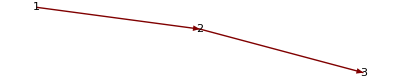
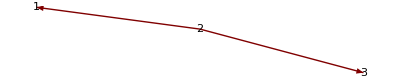
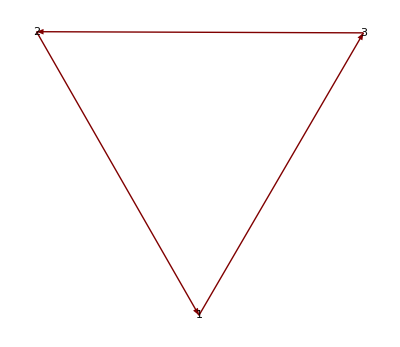
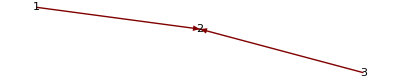
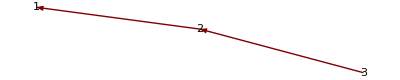
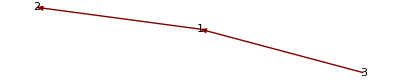
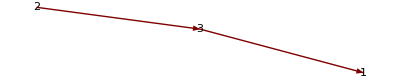
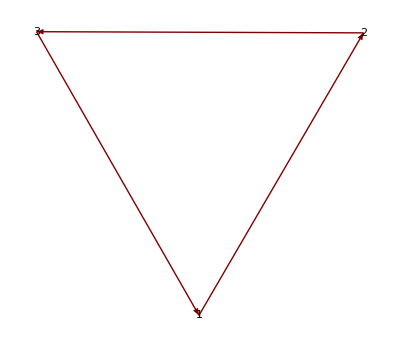
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotQuiver/@bOpts
```

```mathematica
a3[][[6,2]]
```

{{0,-1,0},{1,0,-1},{0,1,0}}

```mathematica
a3[][[1,2]]
```

{{0,1,0},{-1,0,1},{0,-1,0}}

```mathematica
a3[][[1,1]]
```

{x1,x2,x3}

```mathematica
a3[][[6,1]]
```

{1/x1,(x1 x2 (1+x3))/(1+x1),1/x3}

```mathematica
a3Func[x1,x2,x3]-a3Func[1/x3,1/x2,1/x1]//b3c//Expand
```

-tensor[x1,1+x1,x1,x1]+1401+tensor[1+x1+x1 x2+x1 x2 x3,1+x2+x2 x3,1+x1+x1 x2+x1 x2 x3,1+x1+x1 x2+x1 x2 x3]
 |  |  |  |

```mathematica
a2Func[x1,x2]+a2Func[1/x2,1/x1]//b2b2
```

0

```mathematica
sortInverse[Together[d4Xs[x1,x2,x3,x4]]]===sortInverse[Together[d4Xs[1/x3,1/x2,1/x1,x4]]]
```

False

```mathematica
RowReduce[Table[Join[a3[][[6,2,i]],a3[][[1,2,i]]],{i,Length[a3[][[1,2]]]}]]//MatrixForm
```

(1 | 0 | -1 | -1 | 0 | 1
0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
RowReduce[Join[a3[][[7,2]],a3[][[1,2]]]]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
findPerm[b1_,b2_]:=Module[{perms,ret},
perms=Permutations[Range[Length[b1]]];
ret=Select[perms,(Table[b1[[#[[i]],#[[j]]]],{i,Length[b1]},{j,Length[b1]}]==b2)&];
Which[Length[ret]==1,Return[ret[[1]]],Length[ret]==0,Return[{}],Length[ret]>0,Return["ERROR -- TOO MANY PERMUTATIONS"]]];
```

```mathematica
alg=a4[];
```

```mathematica
test[i_,j_]:=With[{perm=findPerm[alg[[j,2]],alg[[i,2]]]},If[Length[perm]>0,(Solve[Table[alg[[i,1,ii]]-(alg[[j,1,perm[[ii]]]]/.{x1->x1p,x2->x2p,x3->x3p,x4->x4p})==0,{ii,Length[alg[[1,1]]]}],{x1,x2,x3,x4}]/.{x1p->x1,x2p->x2,x3p->x3,x4p->x4})[[1]],0]]
```

```mathematica
allPerms=Union[Together[FullSimplify[Union[DeleteCases[test@@@Subsets[Range[Length[alg]],{2}],0]]]]];
```

```mathematica
a3[]
```

{{{x1,x2,x3},{{0,1,0},{-1,0,1},{0,-1,0}},{}},{{1/x1,(x1 x2)/(1+x1),x3},{{0,-1,0},{1,0,1},{0,-1,0}},{1}},{{x1 (1+x2),1/x2,(x2 x3)/(1+x2)},{{0,-1,1},{1,0,-1},{-1,1,0}},{2}},{{x1,x2 (1+x3),1/x3},{{0,1,0},{-1,0,-1},{0,1,0}},{3}},{{x2/(1+x1+x1 x2),(1+x1)/(x1 x2),(x1 x2 x3)/(1+x1+x1 x2)},{{0,1,0},{-1,0,-1},{0,1,0}},{1,2}},{{1/x1,(x1 x2 (1+x3))/(1+x1),1/x3},{{0,-1,0},{1,0,-1},{0,1,0}},{1,3}},{{1/(x1 (1+x2)),(1+x1+x1 x2)/x2,(x1 x2 x3)/(1+x1+x1 x2)},{{0,1,-1},{-1,0,0},{1,0,0}},{2,1}},{{x1 (1+x2+x2 x3),x3/(1+x2+x2 x3),(1+x2)/(x2 x3)},{{0,0,-1},{0,0,1},{1,-1,0}},{2,3}},{{x1 (1+x2+x2 x3),1/(x2 (1+x3)),(1+x2+x2 x3)/x3},{{0,-1,0},{1,0,1},{0,-1,0}},{3,2}},{{x2/(1+x1+x1 x2),((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3),(1+x1+x1 x2)/(x1 x2 x3)},{{0,1,0},{-1,0,1},{0,-1,0}},{1,2,3}},{{(x2 (1+x3))/(1+x1+x1 x2+x1 x2 x3),(1+x1)/(x1 x2 (1+x3)),(1+x1+x1 x2+x1 x2 x3)/((1+x1) x3)},{{0,1,-1},{-1,0,1},{1,-1,0}},{1,3,2}},{{(x2 x3)/((1+x2) (1+x1+x1 x2+x1 x2 x3)),(1+x1+x1 x2)/x2,(1+x1+x1 x2)/(x1 x2 x3)},{{0,1,1},{-1,0,0},{-1,0,0}},{2,1,3}},{{1/(x1 (1+x2+x2 x3)),x3/(1+x2+x2 x3),((1+x2) (1+x1+x1 x2+x1 x2 x3))/(x2 x3)},{{0,0,1},{0,0,1},{-1,-1,0}},{2,3,1}},{{1/(x1 (1+x2+x2 x3)),(1+x1+x1 x2+x1 x2 x3)/(x2 (1+x3)),(1+x2+x2 x3)/x3},{{0,1,0},{-1,0,1},{0,-1,0}},{3,2,1}}}

```mathematica
Length[allPerms]
```

6

```mathematica
Union[allPerms]
```

{{x1→1/x2,x2→x1 (1+x2)},{x1→(x1 x2)/(1+x1),x2→1/x1},{x1→1/(x1 (1+x2)),x2→(1+x1+x1 x2)/x2},{x1→x2/(1+x1+x1 x2),x2→(1+x1)/(x1 x2)}}

```mathematica
sortInverse[Together[a2Xs[]/.{x1->1/x2,x2->1/x1}]]
```

{x1,x2,(x1 x2)/(1+x1),x1 (1+x2),(1+x1+x1 x2)/x2}

```mathematica
pb[a3[]][1/x1,1/x2]
```

ⅈ

```mathematica
a2[]
```

{{{x1,x2},{{0,1},{-1,0}},{}},{{1/x1,(x1 x2)/(1+x1)},{{0,-1},{1,0}},{1}},{{x1 (1+x2),1/x2},{{0,-1},{1,0}},{2}},{{x2/(1+x1+x1 x2),(1+x1)/(x1 x2)},{{0,1},{-1,0}},{1,2}},{{1/(x1 (1+x2)),(1+x1+x1 x2)/x2},{{0,1},{-1,0}},{2,1}}}

```mathematica
allPerms
```

{{x1→x2/(1+x1+x1 x2),x2→((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3),x3→(1+x1+x1 x2)/(x1 x2 x3)},{x1→1/x3,x2→(x1 x2 (1+x3))/(1+x1),x3→1/x1},{x1→(x1 x2 x3)/(1+x1+x1 x2),x2→1/(x1 (1+x2)),x3→(1+x1+x1 x2)/x2},{x1→1/(x1 (1+x2+x2 x3)),x2→(1+x1+x1 x2+x1 x2 x3)/(x2 (1+x3)),x3→(1+x2+x2 x3)/x3},{x1→x3/(1+x2+x2 x3),x2→(1+x2)/(x2 x3),x3→x1 (1+x2+x2 x3)}}

```mathematica
Position[Table[Position[allPerms,Thread[{x1,x2,x3}-> Together[({x1,x2,x3}/.allPerms[[i]])/.allPerms[[j]]]]],{i,5},{j,5}],{}]
```

{{1,4},{2,2},{3,5},{4,1},{5,3}}

```mathematica
Together[({x1,x2,x3}/.allPerms[[3]])/.allPerms[[5]]]
```

{x1,x2,x3}

```mathematica
sortInverse[Together[a3Xs[]/.{x1->x3,x3->x1}]]==sortInverse[a3Xs[]]
```

{x1,x2,(1+x1) x2,(1+x2)/(x1 x2),(1+x2+x1 x2)/x1,x3,(1+x2) x3,(1+x2+x1 x2) x3,(1+x3)/(x2 x3),(1+x3)/((1+x1) x2 x3),(1+x3+x2 x3)/x2,(1+x3+x2 x3)/(x1 x2 x3),(1+x3+x2 x3+x1 x2 x3)/((1+x1) x2),((1+x2) (1+x3+x2 x3+x1 x2 x3))/(x1 x2),(1+x3+x2 x3+x1 x2 x3)/(x1 (1+x3))}=={x1,x2,(x1 x2)/(1+x1),x1 (1+x2),(1+x1+x1 x2)/x2,x3,(x2 x3)/(1+x2),(x1 x2 x3)/(1+x1+x1 x2),x2 (1+x3),(x1 x2 (1+x3))/(1+x1),x1 (1+x2+x2 x3),(1+x2+x2 x3)/x3,(1+x1+x1 x2+x1 x2 x3)/((1+x1) x3),((1+x2) (1+x1+x1 x2+x1 x2 x3))/(x2 x3),(1+x1+x1 x2+x1 x2 x3)/(x2 (1+x3))}

```mathematica
a3[1/x3,1/x2,1/x1]
```

{{{1/x3,1/x2,1/x1},{{0,1,0},{-1,0,1},{0,-1,0}},{}},{{x3,1/(x2 (1+x3)),1/x1},{{0,-1,0},{1,0,1},{0,-1,0}},{1}},{{(1+x2)/(x2 x3),x2,1/(x1 (1+x2))},{{0,-1,1},{1,0,-1},{-1,1,0}},{2}},{{1/x3,(1+x1)/(x1 x2),x1},{{0,1,0},{-1,0,-1},{0,1,0}},{3}},{{x3/(1+x2+x2 x3),x2 (1+x3),1/(x1 (1+x2+x2 x3))},{{0,1,0},{-1,0,-1},{0,1,0}},{1,2}},{{x3,(1+x1)/(x1 x2 (1+x3)),x1},{{0,-1,0},{1,0,-1},{0,1,0}},{1,3}},{{(x2 x3)/(1+x2),(1+x2+x2 x3)/x3,1/(x1 (1+x2+x2 x3))},{{0,1,-1},{-1,0,0},{1,0,0}},{2,1}},{{(1+x1+x1 x2)/(x1 x2 x3),x2/(1+x1+x1 x2),x1 (1+x2)},{{0,0,-1},{0,0,1},{1,-1,0}},{2,3}},{{(1+x1+x1 x2)/(x1 x2 x3),(x1 x2)/(1+x1),(1+x1+x1 x2)/x2},{{0,-1,0},{1,0,1},{0,-1,0}},{3,2}},{{x3/(1+x2+x2 x3),(x2 (1+x3))/(1+x1+x1 x2+x1 x2 x3),x1 (1+x2+x2 x3)},{{0,1,0},{-1,0,1},{0,-1,0}},{1,2,3}},{{((1+x1) x3)/(1+x1+x1 x2+x1 x2 x3),(x1 x2 (1+x3))/(1+x1),(1+x1+x1 x2+x1 x2 x3)/(x2 (1+x3))},{{0,1,-1},{-1,0,1},{1,-1,0}},{1,3,2}},{{(x2 x3)/((1+x2) (1+x1+x1 x2+x1 x2 x3)),(1+x2+x2 x3)/x3,x1 (1+x2+x2 x3)},{{0,1,1},{-1,0,0},{-1,0,0}},{2,1,3}},{{(x1 x2 x3)/(1+x1+x1 x2),x2/(1+x1+x1 x2),((1+x2) (1+x1+x1 x2+x1 x2 x3))/(x2 x3)},{{0,0,1},{0,0,1},{-1,-1,0}},{2,3,1}},{{(x1 x2 x3)/(1+x1+x1 x2),(1+x1+x1 x2+x1 x2 x3)/((1+x1) x3),(1+x1+x1 x2)/x2},{{0,1,0},{-1,0,1},{0,-1,0}},{3,2,1}}}

```mathematica
pb[a3[]][x1/.#,x2/.#]&/@allPerms
```

{1,1,1,1,1}

```mathematica
Length[a3[]]
```

14

```mathematica
Solve[Table[a3[][[1,1,i]]-(a3[][[7,1,findBperm[b1,b2][[i]]]]==0,{i,3}]
```

{x1-(1+x1+x1 x2)/x2,x2-(x1 x2 x3)/(1+x1+x1 x2),-1/(x1 (1+x2))+x3}

```mathematica
b1=a3[][[1,2]];
```

```mathematica
b2=a3[][[7,2]];
```

```mathematica
perms=Permutations[Range[Length[b1]]];
```

```mathematica
perm=perms[[2]]
```

{1,3,2}

```mathematica
b1[[1,2]]
```

1

```mathematica
Select[perms,(Table[b1[[#[[i]],#[[j]]]],{i,Length[b1]},{j,Length[b1]}]==b2)&]
```

{{2,3,1}}

```mathematica
b1
```

{{0,1,0},{-1,0,1},{0,-1,0}}

```mathematica
m2=Table[0,{i,3},{j,3}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
m2[[All,3]]=m[[All,2]]
```

{1,0,0}

```mathematica
m2
```

{{0,0,1},{0,0,0},{0,0,0}}

```mathematica
a3[][[3,2]]//MatrixForm
```

(0 | -1 | 1
1 | 0 | -1
-1 | 1 | 0)

```mathematica
Table[a3[][[1,2]]*a3[][[i,2]]//MatrixForm,{i,Length[a3[]]}]
```

{(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(0 | -1 | 0
-1 | 0 | 1
0 | 1 | 0),(0 | -1 | 0
-1 | 0 | -1
0 | -1 | 0),(0 | 1 | 0
1 | 0 | -1
0 | -1 | 0),(0 | 1 | 0
1 | 0 | -1
0 | -1 | 0),(0 | -1 | 0
-1 | 0 | -1
0 | -1 | 0),(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 1 | 0),(0 | -1 | 0
-1 | 0 | 1
0 | 1 | 0),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 1 | 0),(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0)}

```mathematica
Out[591]*Out[592]
```

{{0,1,0},{1,0,0},{0,0,0}}

```mathematica
sortInverse[Together[a3Xs[]/.Together[Solve[Thread[a3[][[1,1]]-(a3[][[7,1]]/.{x1->x1p,x2->x2p,x3->x3p})==0],{x1,x2,x3}]/.{x1p->x1,x2p->x2,x3p->x3}][[1]]]]==sortInverse[a3Xs[]]
```

False

```mathematica
a3[][[14,1]]
```

{1/(x1 (1+x2+x2 x3)),(1+x1+x1 x2+x1 x2 x3)/(x2 (1+x3)),(1+x2+x2 x3)/x3}

```mathematica
opts=DeleteCases[Position[Table[Length[Complement[Together[(Solve[Thread[a3[][[i,1]]-(a3[][[j,1]]/.{x1->x1p,x2->x2p,x3->x3p})==0],{x1,x2,x3}]/.{x1p->x1,x2p->x2,x3p->x3})//.(a_->b_):>b][[1]],a3Xs[]]],{i,Length[a3[]]},{j,Length[a3[]]}],0],{a_,a_}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{2,3},{2,6},{2,9},{3,6},{4,3},{4,5},{4,6},{5,4},{9,2},{10,1},{10,14},{14,1},{14,10}}

```mathematica
hm[i_,j_]:=sortInverse[Together[a3Xs[]/.Thread[{x1,x2,x3}->FullSimplify[(Solve[Thread[a3[][[i,1]]-(a3[][[j,1]]/.{x1->x1p,x2->x2p,x3->x3p})==0],{x1,x2,x3}]/.{x1p->x1,x2p->x2,x3p->x3})//.(a_->b_):>b][[1]]]]]===sortInverse[a3Xs[]]
```

```mathematica
Position[hm@@@opts,True]
```

{{9},{19},{22},{25},{26}}